```mathematica
Clear["Global`*"]
pitchEXP=Import[NotebookDirectory[]<>"/SPHERIC_TestCase12/Rotation.dat"][[1;;]];
pitchEXP[[1]]
pitchEXP=pitchEXP[[2;;]];
motionsEXP=Import[NotebookDirectory[]<>"/SPHERIC_TestCase12/Motions.dat"][[1;;]];
motionsEXP[[1]]
heaveEXP={#1,#2}&@@@motionsEXP[[2;;,{1,2}]];
surgeEXP=motionsEXP[[2;;,{3,4}]];

name="~/BEM/Hadzic2005_water300/result.json";
jsonText=Import[name,"Text"];
jsonText=StringReplace[jsonText,{"NaN"->"null","nan"->"null"}];
data=ImportString[jsonText,"JSON"];
floatname="floatingbody";
Quiet[heave=(floatname<>"_COM"/.data)[[;;,3]]-(0.4-0.03+0.05/2);];
Quiet[surge=(floatname<>"_COM"/.data)[[;;,1]]+(4.-2.11);];
Quiet[pitch=(floatname<>"_pitch"/.data);];
Quiet[force=(floatname<>"_force"/.data);];
Quiet[area=(floatname<>"_area"/.data);];
Quiet[Vx=(floatname<>"_velocity"/.data)[[;;,1]];];
Quiet[Vy=(floatname<>"_velocity"/.data)[[;;,2]];];
Quiet[Vz=(floatname<>"_velocity"/.data)[[;;,3]];];
Quiet[time=(("simulation_time"/.data)+0.1);];
Quiet[cputime=(("cpu_time"/.data)+0.1);];
Quiet[realtime=(("wall_clock_time"/.data)+0.1);];
(*Kramer20210d03=Import[NotebookDirectory[]<>"Kramer2021_0d3.csv"];*)
H0=30/1000;
```

{Time,(s),Roll,(degrees)}

{Time,(s),Heave,(m),Time,(s),Sway,(m)}

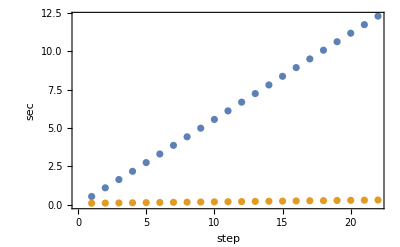

```mathematica
ListPlot[{realtime/60,time}
,Frame->True
,FrameLabel->{"step","sec"}
]
```

```mathematica
realtime
cputime
time
```

{33.0545,66.8021,99.1059,131.197,165.257,198.762,232.466,265.809,299.508,333.584,367.043,401.03,434.443,468.209,501.899,535.857,569.674,603.618,636.758,670.173,703.458,736.709}

{435.952,870.299,1301.21,1731.14,2171.64,2609.21,3047.17,3483.36,3921.34,4358.58,4797.26,5235.4,5675.4,6111.82,6552.22,6991.02,7428.52,7865.82,8303.4,8740.37,9178.01,9617.53}

{0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32}

```mathematica
Column@Table[data[[i]][[1]],{i,1,Length[data]}]
```

cpu_time
floatingbody_COM
floatingbody_EK
floatingbody_EP
floatingbody_accel
floatingbody_area
floatingbody_force
floatingbody_pitch
floatingbody_roll
floatingbody_torque
floatingbody_velocity
floatingbody_yaw
simulation_time
wall_clock_time
water_E
water_EK
water_EP
water_volume

```mathematica
ListPlot[Transpose[{time,force}]]
```

-Graphics-

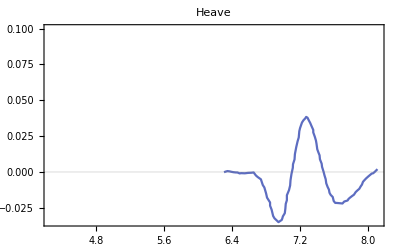

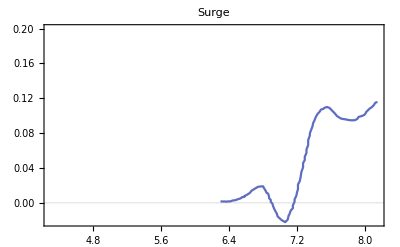

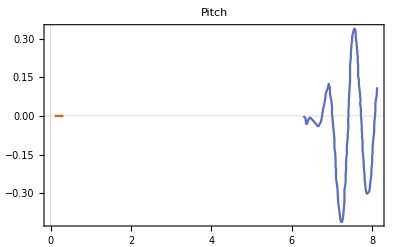

```mathematica
ListPlot[{Transpose[{time,heave}],{#1,#2}&@@@heaveEXP},PlotLabel->"Heave",PlotRange->{All,0.1},Joined->True,PlotTheme->"Scientific"]
ListPlot[{Transpose[{time,surge}],{#1,#2}&@@@surgeEXP},PlotLabel->"Surge",PlotRange->{All,0.2},PlotRange->All,Joined->True,PlotTheme->"Scientific"]
ListPlot[{Transpose[{time,pitch}],{#1,#2/180*Pi}&@@@pitchEXP},PlotLabel->"Pitch",PlotRange->All,Joined->True,PlotTheme->"Scientific"]
```

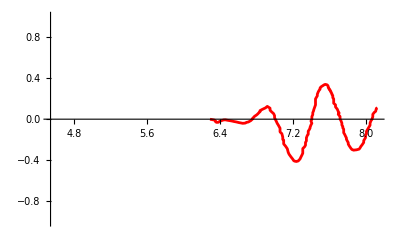

```mathematica
ListPlot[
{Transpose[{time,pitch}],
{#1,#2/180*Pi}&@@@pitchEXP},
PlotStyle->{{Darker[Green],Opacity[0.6]},{Red},{Dashed,Blue,Opacity[0.6]},{Thick}},
Joined->{True,True,True},
PlotRange->{Automatic,{-1,1}}
(*PlotRange->{{0,2.25},{-1.,1.}},*)
(*PlotTheme->"Scientific",
Frame->True,
Mesh->All,
GridLines->{Table[i,{i,0.,4.,0.2}],Table[i,{i,-1.,1.,0.5}]},
Frame->True,
FrameLabel->{Style["t/T",FontSize->20,Italic],Style["H/H_0",FontSize->20,Italic]},
FrameStyle->Directive[FontSize->20,Black,Thickness[0.002]],GridLines->{Table[i,{i,0.,4.,0.2}],Table[i,{i,-1.,1.,0.5}]},GridLinesStyle->Directive[Gray,Dotted],
PlotTheme->"Scientific",
ImageSize->500,
PlotLegends->Placed[LineLegend[{"Measured Data","Simulated Data"},LegendMarkerSize->20,LabelStyle->20],{0.75,0.15}]*)
]
```